# AD Implementation Forward Mode

The forward mode of AD is relatively simple to understand.  This is a brief review of gradients and Jacobians and how forward mode AD works.  Implementation details if time permits.

## Calculus 3 Review

### Partial and Directional Derivatives f:ℝ^n→ℝ

The partial derivative is defined analogously to the calculus one definition
	(∂f)/(∂x_j)=lim_(h→0) (f(x+h e_j)-f(x))/h
it is the slope in the j^th direction.  The directional derivative in the direction u is 
	(∂f)/(∂u)=lim_(h→0) (f(x+h u)-f(x))/h
Calculus 3 usually normalizes directions:  the definition makes sense for non-normalized vectors.  It is computationally better to compute with centered differences
	(∂f)/(∂u)=lim_(h→0) (f(x + h u)-f(x - h u ))/(2h)
Note that (∂f)/(∂x_i):ℝ^n→ℝ.

In calculus 3 you symbolically computed ∂f/∂x_1 by freezing the variables x_2 etc and using calculus one symbolic techniques to differentiate with respect to x_1.

### Gradients f:ℝ^n→ℝ

The gradient is simply the vector of partial derivatives
	∇f=((∂f)/(∂x_1),(∂f)/(∂x_2),… ,(∂f)/(∂x_n))
Note ∇f:ℝ^n→ℝ^n.

Interpretation:
The gradient points in the steepest direction uphill;
The gradient is perpendicular to level surfaces;
At a smooth minimum x of f  we have ∇f(x)=0;
…

```mathematica
Clear[x1,x2,f,delf]
f[{x1_,x2_}]:= Sin[x1 x2 + Cos[x1+4 x2]]+Cos[x2]
delf[{x1_,x2_}]=D[f[{x1,x2}],{{x1,x2}}];
Show[
ContourPlot[f[{x1,x2}],{x1,-3,3},{x2,-3,3},PlotPoints->25],
VectorPlot[delf[{x1,x2}],{x1,-3,3},{x2,-3,3},VectorPoints->Fine,PlotLegends->Automatic],
PlotLabel->f[{x1,x2}]]
```

{Cos[x1 x2+Cos[x1+4 x2]] (x2-Sin[x1+4 x2]),-Sin[x2]+Cos[x1 x2+Cos[x1+4 x2]] (x1-4 Sin[x1+4 x2])}

-Graphics-

### Jacobians f:ℝ^n→ℝ^m

For a vector valued function you just differentiate the m component functions 		
	f=(f_1,f_2,…,f_m)
to get a matrix J (J is for Jacobian) with entries 
	J_(i,k)=(∂f_i)/(∂x_k)
Note: J:ℝ^n→ℝ^(m×n).  You can think of as either a stack of columns  
	J=((∂f)/(∂x_1) (∂f)/(∂x_2) … (∂f)/(∂x_n))
or a pile of rows
	J=(∇f_1
∇f_2
⋮
∇f_m)

In calculus 3 you used the determinant of the Jacobian to compute volume changes for 2D and 3D integrals.  In 2D this area transformation looked like
	dA=det((∂f_1)/(∂x) | (∂f_1)/(∂y)
(∂f_2)/(∂x) | (∂f_2)/(∂y))dx dy

## AD Idea

Computers really just do a lot of arithmetic and a little logic. Arithmetic is differentiable!  Computer program should be differentiable using the sum rule
	(u+v)'=u'+v'
and the product rule
	(u v)'=u'v+u v'.

The question is how to organize differentiating a computer program.  The easiest thing to do is to just include the derivative (using the rules up above) as you go.  You get the following simple extended addition and multiplication rules.  
	(u,du)+(v,dv)=(u+v,u'+v')
and the product rule
	(u, du) ×(v,dv)=(u×v, du×v+u×dv)

For a function of two variables f:ℝ^2→ℝ computing the extended f at the vector with first component (x_1,1)  and second component (x_2,0)  gives f and (∂f)/(∂x_1) at the point x. Computing the extended f at the vector with first component (x_1,0)  and second component (x_2,1)  gives f and (∂f)/(∂x_2) at the point x.  Forward mode AD is just making this process automatic.

## Finite Difference (FD) Approximations

Finite Difference approximations are much less accurate and need to be used with care.

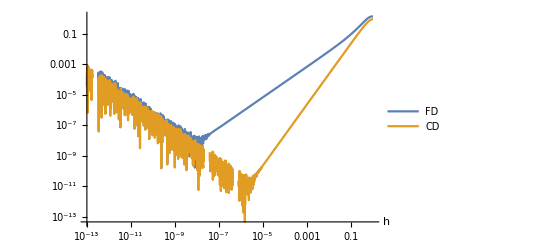

```mathematica
f[x_]:= Sin[x+ Sin[x^2]]
x0=0.5;
LogLogPlot[{f'[x0]-(f[x0+h]-f[x0])/h,f'[x0]-(f[x0+h]-f[x0-h])/(2h)},{h,10^-13,1},AxesLabel->{"h"},
PlotLegends->{"FD","CD"},
PlotRange->All]
```

## Differentiating the SVD

The SVD expresses an m×n matrix as the product
	A=U.Σ.Vᵀ
where U and V are orthogonal and Σ is diagonal. For simplicity lets assume the matrix is square and full rank then the product rule gives
	A'=U'.Σ.Vᵀ+U.Σ'.Vᵀ+U.Σ.Vᵀ'
Since  U and V are orthogonal U.Uᵀ=V.Vᵀ=I. Differentiating the first of these gives
	U.(Uᵀ)'+U'.Uᵀ=0
which means that U'.Uᵀ=-(U'.Uᵀ)ᵀ.  In other words, 
	X=U'.Uᵀ 
is a skew matrix. Similarly we have that 
	Y=V'.Vᵀ
is a skew matrix.

Our goal is to compute the diagonal matrix Σ' and the skew matrices X and Y from A' the diagonal matrix Σ and the orthogonal matrices U and V.  Multiply the product rule expression by Uᵀ and V
	Uᵀ.A'.V=Uᵀ.U'.Σ.Vᵀ.V+Uᵀ.U.Σ'.Vᵀ.V+Uᵀ.U.Σ.Vᵀ'.V
orthogonality means this is  
	Uᵀ.A'.V=Uᵀ.U'.Σ+Σ'+Σ.Vᵀ'.V
the definition of X and Y means this is   
	X.Σ+Σ'+Σ.Y=Uᵀ.A'.V
The diagonal entries of X.Σ and Σ.Y are zero so the diagonal of Σ' matches the diagonal of Uᵀ.A'.V.  I am going to write this as
	σ'=diagonal(Uᵀ.A'.V)
so now we know everything except the skew matrices X and Y. Note that neither X.Σ or Σ.Y are skew! This last part of the equation is a solvable linear equation if you look at it. I am going to write it as
	X.Σ+Σ.Y=B=Uᵀ.A'.V-Σ'
I can transpose the equation to get
	Σᵀ.Xᵀ+Yᵀ.Σᵀ=Bᵀ
or equivalently since X and Y are skew and Σ is diagonal
	-Σ.X-Y.Σ=Bᵀ.
Subtracting I get 
	Σ.(X+Y)+(X+Y).Σ=B-Bᵀ
Adding I get
	(X-Y).Σ-Σ.(X-Y)=B-Bᵀ
Defining Zp=X+Y and Zm=X-Y we get the two separate equations
	Zp.Σ+Σ.Zp=B-Bᵀ
and 
	Zm.Σ-Σ.Zm=B+Bᵀ
These are diagonal Sylvester/Lyapunov equations.  They have a solution you can just write down!

```mathematica
m=3;{X,Y}=RandomReal[{-1,1},{2,m,m}];X=X-Xᵀ;Y=Y-Yᵀ;
Dia=DiagonalMatrix[RandomReal[{0.1,1},m]];
Map[MatrixForm,{Dia.X, Y.Dia}]
```

{(0. | -0.403506 | -0.995718
0.581152 | 0. | -0.695707
1.37443 | 0.666765 | 0.),(0. | 0.622464 | -0.0677944
-0.432189 | 0. | -0.574138
0.0491143 | 0.599059 | 0.)}

```mathematica
m=3;
Z=Array[z,{m,m}];
σs=Array[σ,m];
Σ=DiagonalMatrix[σs];
Kp=Km=ConstantArray[0,{m,m}];
Do[Kp⟦i,j⟧=If[ i==j,0,1/(σs⟦j⟧+σs⟦i⟧)],{i,m},{j,m}]
Do[Km⟦i,j⟧=If[ i==j,0,1/(σs⟦j⟧-σs⟦i⟧)],{i,m},{j,m}]
Map[MatrixForm,{Simplify[Kp(Z.Σ+Σ.Z)],Simplify[Km(Z.Σ-Σ.Z)],Z}]
```

{(0 | z[1,2] | z[1,3]
z[2,1] | 0 | z[2,3]
z[3,1] | z[3,2] | 0),(0 | z[1,2] | z[1,3]
z[2,1] | 0 | z[2,3]
z[3,1] | z[3,2] | 0),(z[1,1] | z[1,2] | z[1,3]
z[2,1] | z[2,2] | z[2,3]
z[3,1] | z[3,2] | z[3,3])}

## Differentiating a Schur Decomposition

The Schur decomposition of a matrix A is 
	A=Q.T.Qᵀ or equivalently T=Qᵀ.A.Q
where Q is orthogonal (Q.Qᵀ=I) and T is upper triangular. Differentiating gives
	A'=Q'.T.Qᵀ+Q.T'.Qᵀ+Q.T.(Qᵀ)' 
and 
	Q'.Qᵀ+Q.(Qᵀ)'=0

```mathematica
m=4;
A=RandomReal[{-1,1},{m,m}];
{Q,T}=SchurDecomposition[A];
Map[Norm,{A-Q.T.Qᵀ,Q.Qᵀ}]
```

{3.97528×10^-15,1.}